# Plasma Imaging

## Sample plot

```mathematica
(* -- import -- *)
nb=NotebookDirectory[];
raw=Import[nb<>"data/290/dilute.mx"];
gf=Show[raw[[30]],ImageSize->800,AspectRatio->.287,Frame->True,FrameTicks->None,FrameStyle->Directive[Black,AbsoluteThickness[.5]]]
```

-Graphics-

## Movie

## Annotations

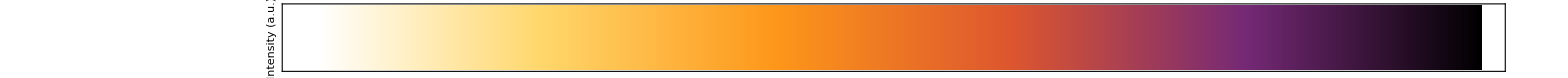

```mathematica
(* -- initialize -- *)
If[Length@Kernels[]≤1,LaunchKernels[]];
Clear[lb,r,annotTime,annotState,annotScale,annotLaserDirection,annotLaserEnvelope,annotAxis];

(* -- annotation 1: elapsed time from laser shot -- *)
annotTime[time_:1]:=Graphics[
Text[Framed[Style[
"t = "<>ToString[time]<>" (ns)",
FontFamily->"Arial",
FontSize->30,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{20,20}r,{-1,-1}]];

(* -- annotation 2: state -- *)
annotState=Graphics[{
Text[Framed[Style[
lb,
FontFamily->"Arial",
FontSize->30,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{20,294-20}r,{-1,1}]
}];

(* -- annotation 3: scale -- *)
annotScale=Graphics[{
{AbsoluteThickness[3],Black,
Line[{{1024-20-120,294-20},{1024-20,294-20}}r]},
Text[Framed[Style[
"2 mm",
FontFamily->"Arial",
FontSize->30,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{1024-20,294-20}r,{1,1}]
}];

(* -- annotation 4: laser direction -- *)
annotLaserDirection=Graphics[{
(* -- direction -- *)
{AbsoluteThickness[3],Gray,
Arrowheads[Large],Arrow[{{600,20},{600-200,20}}r]},
Text[Framed[Style[
"Laser",
FontFamily->"Arial",
FontSize->30,
FontColor->Gray],
FrameStyle->Transparent,
Background->Transparent],
{500,20}r,{0,-1}]
}];

(* -- annotation 5: laser envelope -- *)
annotLaserEnvelope=Graphics[{
{AbsoluteThickness[1.5],AbsoluteDashing[8],Gray,
Line[{{1,147+15.6},{141,147+4},{194,147+4},{1023,147+72.5}}r],
Line[{{1,147-15.6},{141,147-4},{194,147-4},{1023,147-72.5}}r]}
}];

(* -- annotation 6: axis -- *)
annotAxis=Graphics[{
{AbsoluteThickness[3],Black,
Arrowheads[Large],Arrow[{{700,15},{700,294-15}}r]},
Text[Framed[Style[
"r (mm)",
FontFamily->"Arial",
FontSize->30,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{685,294}r,{1,-1},{0,1}],
Table[Text[Framed[Style[
ToString[i],
FontFamily->"Arial",
FontSize->30,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{720,147+70i}r,{0,1},{0,1}],{i,-1,1}],
Table[{AbsoluteThickness[1.5],Black,
Line[{{690,147+60i},{710,147+60i}}r]}
,{i,-1,1}]
}];

(* -- annotation 7: crosshair -- *)
annotCrosshair=Graphics[{
{AbsoluteThickness[3],Red,Line[{{700-20,147},{700+20,147}}r],Line[{{700,147-20},{700,147+20}}r]},
{AbsoluteThickness[3],Red,Line[{{700-20,147},{700+20,147}}r],Line[{{700,147-20},{700,147+20}}r]},
{EdgeForm[Transparent],FaceForm[Red],Disk[{700,147}r,12r]},
{EdgeForm[Transparent],FaceForm[White],Disk[{700,147}r,6r]}
}];

(* -- custom bar legend -- *)
customColorize=Compile[value,
Module[
{c1,c2,c3,c4,c5,c6},
{c1,c2,c3,c4,c5,c6}={{1.,1.,1.},{1.,0.8423264,0.4188294},{0.9917508,0.5901996,0.09831576},{0.8647229999999999,0.3364763999999999,0.1829199600000001},{0.4558917999999999,0.16060319999999997,0.4593580000000001},{0.,0.,0.}};
Which[value<.01,{1,1,1},value<0.2,c1+(c2-c1) ((value-.01)/(0.2-.01)),value<0.4,c2+(c3-c2) ((value-0.2)/0.2),value<0.6,c3+(c4-c3) ((value-0.4)/0.2),value<.8,c4+(c5-c4)((value-0.6)/0.2),True,c5+(c6-c5)((value-.8)/.2)]
],
Parallelization->True,RuntimeAttributes->{Listable},CompilationTarget->"C"];

barLegend=Graphics[

Raster[{Table[customColorize[x],{x,0,1,.001}]},{{0,0},{1,1}}],

PlotRange->{{0,1},{0,1}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->30,FontWeight->Plain},

Frame->True,
FrameTicks->{{None,None},{None,Table[{i,Text[Style[StringForm["`1` ",i],TextAlignment->Left]],{.02,0}},{i,0,1}]}},
FrameLabel->{{"Intensity (a.u.)",None},{None,None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],
RotateLabel->False,

GridLines->None,
ImageSize->1600,AspectRatio->.05,
ImagePadding->{{800+.5,.5},{5,40}}

]
```

## Append images

```mathematica
(* -- initialize -- *)
nb=NotebookDirectory[];

(* -- images -- *)
imgs=Table[

(* -- import -- *)
raw=Import[nb<>"data/"<>ToString@filter<>"/"<>state<>".mx"];

(* -- info -- *)
time=Join[Range[-15,50],{100,200,400,1000}];
ratio=Which[filter==290,1,filter==700,.859];
label=Which[state=="dense","Inhomogeneous",state=="dilute","Homogeneous"]<>Which[filter==290," (290+ ± 13 nm)",filter==700," (700+ ± 25 nm)"];

(* -- append annotation -- *)
imgAnnot=ParallelTable[

Show[

raw[[fr]],

{annotTime[time[[fr]]],
annotState,
annotScale,
annotLaserDirection,
annotLaserEnvelope,
annotAxis,
annotCrosshair},

Frame->True,
FrameTicks->None,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],

ImageSize->800,
AspectRatio->.287

]/.{lb->label,r->ratio}

,{fr,Length@raw}];

imgAnnot

,{state,{"dense","dilute"}},{filter,{290,700}}];

imgsGrid=Thread[Grid[Transpose[imgs,{2,3,1}],Spacings->{.5,.5}]];

(* -- retarded frames -- *)
retard=Flatten[Table[ConstantArray[imgsGrid[[i]],5],{i,-5,-1}],1];
frames=Join[imgsGrid[[;;-6]],retard];

framesColorbar=Column[{barLegend,#},{Right}]&/@frames;

(* -- export -- *)
Export[nb<>"movie.mov",framesColorbar,"FrameRate"->5,"VideoEncoding"->"H264"];
```

## Images grid

## Annotations

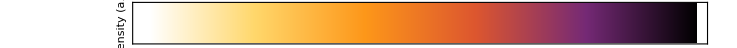

```mathematica
(* -- initialize -- *)
If[Length@Kernels[]≤1,LaunchKernels[]];
Clear[lb,r,annotTime,annotState,annotScale,annotLaserDirection,annotLaserEnvelope,annotAxis];

(* -- annotation 1: elapsed time from laser shot -- *)
annotTime[time_:1]:=Graphics[
Text[Framed[Style[
"t = "<>ToString[time]<>" (ns)",
FontFamily->"Arial",
FontSize->14,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{20,20}r,{-1,-1}]];

(* -- annotation 2: state -- *)
annotState=Graphics[{
Text[Framed[Style[
lb,
FontFamily->"Arial",
FontSize->14,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{20,294-20}r,{-1,1}]
}];

(* -- annotation 3: scale -- *)
annotScale=Graphics[{
{AbsoluteThickness[3],Black,
Line[{{1024-20-120,294-20},{1024-20,294-20}}r]},
Text[Framed[Style[
"2 mm",
FontFamily->"Arial",
FontSize->14,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{1024-20,294-20}r,{1,1}]
}];

(* -- annotation 4: laser direction -- *)
annotLaserDirection=Graphics[{
(* -- direction -- *)
{AbsoluteThickness[3],Gray,
Arrowheads[Large],Arrow[{{600,20},{600-200,20}}r]},
Text[Framed[Style[
"Laser",
FontFamily->"Arial",
FontSize->14,
FontColor->Gray],
FrameStyle->Transparent,
Background->Transparent],
{500,20}r,{0,-1}]
}];

(* -- annotation 5: laser envelope -- *)
annotLaserEnvelope=Graphics[{
{AbsoluteThickness[1.5],AbsoluteDashing[8],Gray,
Line[{{1,147+15.6},{141,147+4},{194,147+4},{1023,147+72.5}}r],
Line[{{1,147-15.6},{141,147-4},{194,147-4},{1023,147-72.5}}r]}
}];

(* -- annotation 6: axis -- *)
annotAxis=Graphics[{
{AbsoluteThickness[3],Black,
Arrowheads[Large],Arrow[{{700,15},{700,294-15}}r]},
Text[Framed[Style[
"r (mm)",
FontFamily->"Arial",
FontSize->14,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{685,294}r,{1,-1},{0,1}],
Table[Text[Framed[Style[
ToString[i],
FontFamily->"Arial",
FontSize->14,
FontColor->Black],
FrameStyle->Transparent,
Background->Transparent],
{720,147+70i}r,{0,1},{0,1}],{i,-1,1}],
Table[{AbsoluteThickness[1.5],Black,
Line[{{690,147+60i},{710,147+60i}}r]}
,{i,-1,1}]
}];

(* -- annotation 7: crosshair -- *)
annotCrosshair=Graphics[{
{AbsoluteThickness[3],Red,Line[{{700-20,147},{700+20,147}}r],Line[{{700,147-20},{700,147+20}}r]},
{AbsoluteThickness[3],Red,Line[{{700-20,147},{700+20,147}}r],Line[{{700,147-20},{700,147+20}}r]},
{EdgeForm[Transparent],FaceForm[Red],Disk[{700,147}r,12r]},
{EdgeForm[Transparent],FaceForm[White],Disk[{700,147}r,6r]}
}];

(* -- custom bar legend -- *)
customColorize=Compile[value,
Module[
{c1,c2,c3,c4,c5,c6},
{c1,c2,c3,c4,c5,c6}={{1.,1.,1.},{1.,0.8423264,0.4188294},{0.9917508,0.5901996,0.09831576},{0.8647229999999999,0.3364763999999999,0.1829199600000001},{0.4558917999999999,0.16060319999999997,0.4593580000000001},{0.,0.,0.}};
Which[value<.01,{1,1,1},value<0.2,c1+(c2-c1) ((value-.01)/(0.2-.01)),value<0.4,c2+(c3-c2) ((value-0.2)/0.2),value<0.6,c3+(c4-c3) ((value-0.4)/0.2),value<.8,c4+(c5-c4)((value-0.6)/0.2),True,c5+(c6-c5)((value-.8)/.2)]
],
Parallelization->True,RuntimeAttributes->{Listable},CompilationTarget->"C"];

barLegend=Graphics[

Raster[{Table[customColorize[x],{x,0,1,.001}]},{{0,0},{1,1}}],

PlotRange->{{0,1},{0,1}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

Frame->True,
FrameTicks->{{None,None},{None,Table[{i,Text[Style[StringForm["`1` ",i],TextAlignment->Left]],{.02,0}},{i,0,1}]}},
FrameLabel->{{"Intensity (a.u.)",None},{None,None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],
RotateLabel->False,

GridLines->None,
ImageSize->(130*2)*(72/25.4),AspectRatio->.05,
ImagePadding->{{130*(72/25.4)+.5,.5},{5,25}}

]
```

## Append images

```mathematica
(* -- initialize -- *)
nb=NotebookDirectory[];

(* -- images -- *)
imgs=Table[

(* -- import -- *)
raw=Import[nb<>"data/"<>ToString@filter<>"/"<>state<>".mx"];

(* -- info -- *)
time=Join[Range[-15,50],{100,200,400,1000}];
ratio=Which[filter==290,1,filter==700,.859];
label=Which[state=="dense","Inhomo.",state=="dilute","Homo."]<>Which[filter==290," (290+ ± 13 nm)",filter==700," (700+ ± 25 nm)"];

(* -- append annotation -- *)
imgAnnot=Table[

Show[

raw[[fr]],

{annotTime[time[[fr]]],
annotLaserEnvelope},

If[MemberQ[{1,4,17,66},fr],
{annotState,annotScale,annotLaserDirection,annotAxis},
Graphics[]
],

{annotCrosshair},

Frame->True,
FrameTicks->None,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],

ImageSize->130*(72/25.4),
AspectRatio->.287

]/.{lb->label,r->ratio}

,{fr,Length@raw}];

imgAnnot

,{filter,{290,700}},{state,{"dense","dilute"}}];

(* -- selected images -- *)
Do[
(* -- retarded frames -- *)
(*filter="700";*)
idx1=<|"290"->1,"700"->2|>;
(*phase="gen";*)
idx2=<|"gen"->Range[4,16,3],"SCP"->{17,21,26,36,46},"ext"->Range[66,70]|>;
imgsGrid=Grid[{
Join[{barLegend},imgs[[idx1[filter],1,idx2[phase]]]],
Join[{SpanFromLeft},imgs[[idx1[filter],2,idx2[phase]]]]
}ᵀ,Spacings->.5,Alignment->{Right}];

(*Print[imgsGrid];*)

(* -- export -- *)
Export[nb<>ToString@StringForm["`1``2`.pdf",filter,phase],imgsGrid];

,{filter,{"290","700"}},{phase,{"gen","SCP","ext"}}];
```